Computing the Green’s function and errors

```mathematica
ClearAll["Global *"];
path =FileNameJoin[{NotebookDirectory[]},"classical.txt"];
sol = ReadList[path,Number];
n =Length[sol]; (*Import the classical field made in python*)

xmin=0.01; (*Use same minimum and stepsize as used in the python file*)
dx=0.01;
xmax=xmin+(n-1)*dx;
xvals=Table[xmin+(i-1)*dx,{i,1,n}];

CFieldInterpolate = Interpolation[Transpose[{xvals,sol}], InterpolationOrder->3]; (*Make sure to Interpolate the function otherwise you cannot manipulate it*)
Cfield[x_?NumericQ] :=CFieldInterpolate[x];
g[r_?NumericQ] := -2.25-2.5Tanh[(5-r)/0.2]-3*(Cfield[r]^2); (*All the other terms from the Green's function equation with density approximated as a tanh*)

RenormalF[l_,xpnt_?NumericQ]:= Module[{inner,outer,inner1, outer1, inner1prime,outer1prime,fInner,fOuter, fInnerp, fOuterp, fWrons, fGr,r,innerinf,outerinf,inner2,outer2,inner2p,outer2p,infInner,infOuter, infInnerp,infOuterp,infWrons,infGr },

(*First compute the solutions to the transformed equation, need to solve it in the transformed case first as outer solution will be effectively 0 otherwise*)
(*Transformed as w(r)= ln(rf(r), where f(r) is the solution to the original equation, because it makes boundary condition O(1))*)inner=NDSolveValue[{w''[r]+(w'[r])^2-(l(l+1))/r^2+g[r]==0, w[xmin] == (l+1)*Log[xmin], w'[xmin]== (l+1)/xmin},w,{r,xmin,xmax}];
outer = NDSolveValue[{w''[r]+(w'[r])^2-(l(l+1))/r^2+g[r]==0, w[xmax]==-(0.5^0.5)*xmax+Log[xmax], w'[xmax]==-(0.5^0.5)+1/xmax}, w,{r,xmin,xmax}];

inner1=inner[#]&; (*Create inner and outer +derivatives to make transforming back easier*)
outer1= outer[#]&;
inner1prime= inner'[#]&;
outer1prime= outer'[#]&;

fInner= (Exp[inner1[#]]/#)&; (*Transform back into solutions of the original ODE*)
fOuter= (Exp[outer1[#]]/#)&;
fInnerp= (inner1prime[#]*fInner[#]-fInner[#]/#)&;
fOuterp= (outer1prime[#]*fOuter[#]-fOuter[#]/#)&;
fWrons=((fInner[#]*fOuterp[#]-fOuter[#]*fInnerp[#])*(#^2))&;
fGr= (fInner[#]*fOuter[#]/fWrons[#])&;

(*Compute the same process for the constant mass case*)
innerinf=NDSolveValue[{w''[r]+(w'[r])^2-(l(l+1))/r^2-0.5==0, w[xmin] == (l+1)*Log[xmin], w'[xmin]== (l+1)/xmin},w,{r,xmin,xmax}];
outerinf = NDSolveValue[{w''[r]+(w'[r])^2-(l(l+1))/r^2-0.5==0, w[xmax]==-(0.5^0.5)*xmax+Log[xmax], w'[xmax]==-(0.5^0.5)+1/xmax}, w,{r,xmin,xmax}];

inner2 = innerinf[#]&;
outer2 = outerinf[#]&;
inner2p = innerinf'[#]&;
outer2p = outerinf'[#]&;

infInner= (Exp[inner2[#]]/#)&;
infOuter= (Exp[outer2[#]]/#)&;
infInnerp= (inner2p[#]*infInner[#]-infInner[#]/#)&;
infOuterp= (outer2p[#]*infOuter[#]-infOuter[#]/#)&;
infWrons=((infInner[#]*infOuterp[#]-infOuter[#]*infInnerp[#])*(#^2))&; (*x^2 appears due to the spherical coordinates, change for other systems/schemes *)
infGr= (infInner[#]*infOuter[#]/infWrons[#])&; (*coincidence limit Greens function*)

fGr[xpnt](*-infGr[xpnt]*)
];

(*Can take out parts of the code to construct the separate Green's functions- just remember to use numeric wrappers to get the functions to plot. *)
(*I would recommend writing the renormalised field to a text file as it takes a long time to sum up over l*)
```

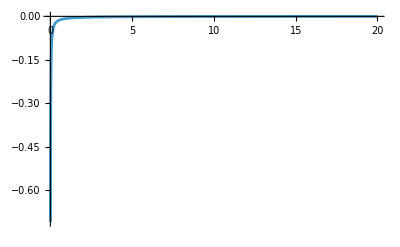

```mathematica
Plot[RenormalF[70,x],{x,xmin,20},PlotRange->All]
```